```mathematica
docker={4.43649,4.00723,3.17904,6.42208,2.6013,4.47281,8.45564,13.232,3.23331,2.67201}

quemu={52.45,52.35,51.463,53.164,49.305,49.525,51.532,53.273,49.91,51.226};

xen={0.476,0.421,0.684,0.522,0.512,0.504,0.513,0.501,0.532,0.526};
```

{4.43649,4.00723,3.17904,6.42208,2.6013,4.47281,8.45564,13.232,3.23331,2.67201}

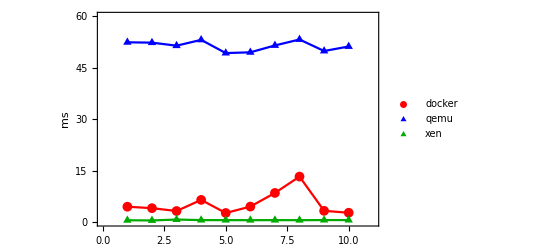

```mathematica
bench1 = ListPlot[{docker,quemu, xen}, PlotLegends->Placed[{"docker","qemu", "xen"}, Top], PlotMarkers->{{●,10},{▲,10}, {▲,10}},PlotJoined->True, PlotStyle->{Red,Blue, Darker[Green]
}, Frame->True,FrameLabel->{,ms}, FrameStyle->Directive[Gray,12], PlotRange->{{0,11},{0,60}}]
```

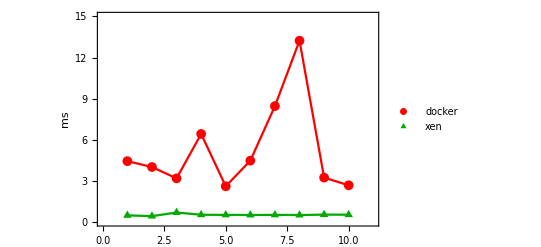

```mathematica
bench2 = ListPlot[{docker,xen}, PlotLegends->Placed[{"docker","xen"}, Top], PlotMarkers->{{●,10},{▲,10}},PlotJoined->True, PlotStyle->{Red, Darker[Green]
}, Frame->True,FrameLabel->{,ms}, FrameStyle->Directive[Gray,12], PlotRange->{{0,11},{0,15.0}}]
```